# Patterns

## Patterns are awesome

## Some examples

### Definitions

```mathematica
f[x_]:= x^2
```

```mathematica
g[x_?OddQ]:="Odd."
g[x_?EvenQ]:= "Multiple of two."
```

### Replacement Rules

```mathematica
a x^4+b x^3+c x^2+d x + e/. x^n_:> x^(n+1)
```

e+d x+c x^3+b x^4+a x^5

### Collect

```mathematica
Collect[(Sin[x]+Cos[y]+1)^10,Sin[_],Simplify]
```

(1+Cos[y])^10+5120 Cos[y/2]^18 Sin[x]+11520 Cos[y/2]^16 Sin[x]^2+15360 Cos[y/2]^14 Sin[x]^3+13440 Cos[y/2]^12 Sin[x]^4+8064 Cos[y/2]^10 Sin[x]^5+3360 Cos[y/2]^8 Sin[x]^6+960 Cos[y/2]^6 Sin[x]^7+180 Cos[y/2]^4 Sin[x]^8+10 (1+Cos[y]) Sin[x]^9+Sin[x]^10

### List Manipulation

```mathematica
tab=Table[{i,i^2},{i,1 ,100}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289},{18,324},{19,361},{20,400},{21,441},{22,484},{23,529},{24,576},{25,625},{26,676},{27,729},{28,784},{29,841},{30,900},{31,961},{32,1024},{33,1089},{34,1156},{35,1225},{36,1296},{37,1369},{38,1444},{39,1521},{40,1600},{41,1681},{42,1764},{43,1849},{44,1936},{45,2025},{46,2116},{47,2209},{48,2304},{49,2401},{50,2500},{51,2601},{52,2704},{53,2809},{54,2916},{55,3025},{56,3136},{57,3249},{58,3364},{59,3481},{60,3600},{61,3721},{62,3844},{63,3969},{64,4096},{65,4225},{66,4356},{67,4489},{68,4624},{69,4761},{70,4900},{71,5041},{72,5184},{73,5329},{74,5476},{75,5625},{76,5776},{77,5929},{78,6084},{79,6241},{80,6400},{81,6561},{82,6724},{83,6889},{84,7056},{85,7225},{86,7396},{87,7569},{88,7744},{89,7921},{90,8100},{91,8281},{92,8464},{93,8649},{94,8836},{95,9025},{96,9216},{97,9409},{98,9604},{99,9801},{100,10000}}

```mathematica
Cases[tab,{_?PrimeQ,_}]
```

{{2,4},{3,9},{5,25},{7,49},{11,121},{13,169},{17,289},{19,361},{23,529},{29,841},{31,961},{37,1369},{41,1681},{43,1849},{47,2209},{53,2809},{59,3481},{61,3721},{67,4489},{71,5041},{73,5329},{79,6241},{83,6889},{89,7921},{97,9409}}

## Basic Patterns

### Blank

```mathematica
Blank[] or _
```

Any one mathematica object i.e. foo[...].

```mathematica
MatchQ[Foo[{1,djd, 2jkdf}],_]
```

True

### Blank with Head specification

```mathematica
Blank[h] or _h
```

Any one mathematica object  with Head h i.e. h[ ...].

```mathematica
MatchQ[Foo[{1,djd, 2jkdf}],_h]
```

False

```mathematica
MatchQ[h[{1,djd, 2jkdf}],_h]
```

True

```mathematica
Clear[f]
f[x_Integer]:=True
f[1]
f[1.5]
```

True

f[1.5]

### BlankSequence

```mathematica
BlankSequence[] or __
```

Any sequence of one or more mathematica objects.

```mathematica
Clear[f]
```

```mathematica
f[x__]:= Plus[x]
```

```mathematica
f[1]
```

1

```mathematica
f[x,y,({{1, 2, 3}, {5, 3, 6}})]
```

{{1+x+y,2+x+y,3+x+y},{5+x+y,3+x+y,6+x+y}}

```mathematica
x+y+({{1, 2, 3}, {5, 3, 6}})
```

{{1+x+y,2+x+y,3+x+y},{5+x+y,3+x+y,6+x+y}}

### Naming Patterns

```mathematica
Pattern[x , _]
x:_
x_
```

Useful if the matched pattern is to be used in a definition or replacement rule. (Use delayed Set (:=) and delayed replace :>

```mathematica
Clear[f]
f[x_]:= x+x^2
2 x+3 x^2/.n_Integer:> n+1
```

3 x+4 x^3

### Alternatives

```mathematica
Alternatives[pattern1,pattern2,pattern3,...]
pattern1|pattern2|pattern3|...
```

Matches anything that matches any of the patterns pattern1, pattern2, pattern3, etc.

```mathematica
Clear[f];
f[1|2]:=0
f[x_]:=x
Table[{i,f[i]},{i,1,5}]
```

{{1,0},{2,0},{3,3},{4,4},{5,5}}

## Conditional Patterns

### PatternTest

```mathematica
x_?test
```

Only matches objects x for which test[x] yields true.

```mathematica
Clear[f];
f[x_?OddQ]:=x+1
f[x_]:=x
Table[{i,f[i]},{i,1,6}]
```

{{1,2},{2,2},{3,4},{4,4},{5,6},{6,6}}

### Condition

```mathematica
f[x_,y_]/;x==y:=0
f[x_,y_]:=x+y
Table[f[i,j],{i,1,4},{j,1,4}]//MatrixForm
```

(0 | 3 | 4 | 5
3 | 0 | 5 | 6
4 | 5 | 0 | 7
5 | 6 | 7 | 0)

### Default values

```mathematica
x_:a
```

Pattern with default value a if omitted.

```mathematica
Clear[f]
f[x_:1]:=x
f[]
```

1

## Applications

### Create "functions" with separate cases

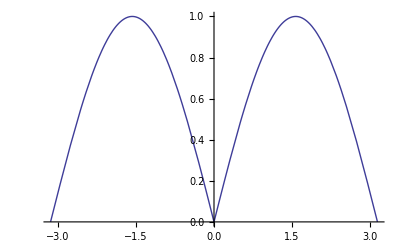

```mathematica
Clear[f]
f[x_?(#>0&)]:=Sin[x]
f[x_?(#<0&)]:=f[-x]
f[0.]:=1
Plot[f[x],{x,-5,5},PlotRange->{0,All}]
```

### Intricate replacements

```mathematica
Clear[f]
```

```mathematica
f[x] DiracDelta'[x-5]
```

f[x] DiracDelta'[-5+x]

```mathematica
f[x] DiracDelta'[x-5]/.
{Longest[a_] DiracDelta'[x+b_]:> -(D[a,x]/.x->-b)DiracDelta[x+b]+(a/.x->-b)DiracDelta'[x+b]}
```

f[5] DiracDelta'[-5+x]-DiracDelta[-5+x] f'[5]